# Rapport Projekt 1

Kurskod: IX1501
Datum: 2017-11-14

Evan Saboo, saboo@kth.se
Max Kufa, mkufa@kth.se

Uppgift 1: Att vinna en Teddy

## Sammanfattning

### Uppgift

Den första uppgiften består av fyra deluppgifter som inkluderar ett tärningsspel med chansen att vinna en Teddy.
Tärningsspelet består av fem olika tärningar (d4, d6, d8, d12 och d20 tärningar). Om summan av alla tärningar, X, har ett värde under 10 eller över 45, så vinner man Teddyn.

De fyra deluppgifterna är följande:

Finn den exakta probabilitetsfunktionen av summan.

Bestäm den exakta probabiliteten att vinna Teddyn. Ge även svaret med flyttalsvärde.

Bestäm den förväntade investeringen som krävs för att vinna Teddyn.

Vad är probabiliteten att vinna en Teddy om man spelar tjugo gånger?

### Resultat

#### Finn den exakta probabilitetsfunktionen av summan

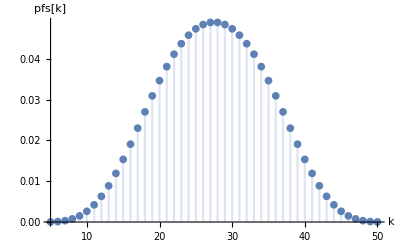
För att få fram probabilitetsfunktionen krävs det att de olika utfallen för all tärningsslag summeras ihop till en enda stokastisk variabel. Summering av stokastiska variabler kallas för “Convolution”. Genom att använda den färdiga formeln DiscreteConvolve så kan vi snabbt och enklet beräkna den sammanlagda stokastiska variabeln för alla tärningar som en funktion:

Piecewise[{{1/46080, s==5||s==50}, {1/9216, s==6||s==49}, {1/3072, s==7||s==48}, {7/9216, s==8||s==47}, {23/15360, s==9||s==46}, {121/46080, s==10||s==45}, {97/23040, s==11||s==44}, {29/4608, s==12||s==43}, {409/46080, s==13||s==42}, {61/5120, s==14||s==41}, {707/46080, s==15||s==40}, {293/15360, s==16||s==39}, {53/2304, s==17||s==38}, {311/11520, s==18||s==37}, {95/3072, s==19||s==36}, {1597/46080, s==20||s==35}, {39/1024, s==21||s==34}, {379/9216, s==22||s==33}, {1007/23040, s==23||s==32}, {211/4608, s==24||s==31}, {1091/23040, s==25||s==30}, {223/4608, s==26||s==29}, {1127/23040, 26<s<29}, {0, True}}]

Funktionen kan även plottas för att ge en klarare bild av dess beteende.

-Graphics-

#### Bestäm den exakta probabiliteten att vinna Teddyn. Ge även svaret med flyttalsvärde

För att vinna Teddyn så behöver man enbart beräkna den sammanlagda probabiliteten av vinstchanserna. Då vi redan beräknat den sammanlagda funktionen så blir det tämligen simpelt. Man adderar probabiliteterna mellan 5≤k≤10 och 45≤k≤50, vilket ger det exakta svaret 41/3840. Numeriskt blir värdet 0.0106771, vilket kan tolkas som att det är strax över en procents chans att man vinner Teddyn.

#### Bestäm den förväntade investeringen som krävs för att vinna Teddyn.

Vi kan jämföra denna uppgift med en vanlig tärning. Alla sidor har 1/6 chans att dyka upp. Därmed kan man förvänta sig att man får sin önskade sida efter sex kast. Matematiskt kan man skriva det som 1/1/6 = 6.
Med samma logik kan man beräkna investeringen som krävs för att vinna Teddyn. Det finns en  41/3840 chans att vinna Teddyn. Därmed kräv det 1/41/3840 antal kast för att vinna Teddyn.

1/41/3840=3840/41=93.6585≈94 kast

Eftersom varje kast kostar 2 Euro så blir den förväntade investeringen 188 euro.

#### Vad är probabiliteten att vinna en Teddy om man spelar tjugo gånger?

Genom att ta den sammanlagda summan av alla utfall (100% eller 1) och subtrahera förlustchansen för 20 kast så kan vi beräkna vinstchansen för 20 kast: 1-((1- p)^20) =0.1932...
Vilket kan tolkas som ~20% att vinna teddyn om man spelar 20 gånger, vilket passar in på vår tidigare beräkning i den föregående uppgiften, då ett kast har en cirka 1% chans att vinna Teddyn.

## Kod

#### Uppgift 1

```mathematica
ClearAll["`*"]
```

Sannolikheten för varje tärning:

```mathematica
Ppf1[k_]:=Piecewise[{{1/4, 1≤ k ≤ 4}},0  (* default *)];
Ppf2[k_]:=Piecewise[{{1/6, 1≤ k ≤ 6}},0  (* default *)];
Ppf3[k_]:=Piecewise[{{1/8, 1≤ k ≤ 8}},0  (* default *)];
Ppf4[k_]:=Piecewise[{{1/12, 1≤ k ≤ 12}},0  (* default *)];
Ppf5[k_]:=Piecewise[{{1/20, 1≤ k ≤ 20}},0  (* default *)];
```

Sannolikheterna för summorna av tärningarna kan beräknas genom DiscreteConvolve:

```mathematica
x1[s_]=DiscreteConvolve[Ppf1[k],Ppf2[k],k,s];
x2[s_]=DiscreteConvolve[x1[k],Ppf3[k],k,s];
x3[s_]=DiscreteConvolve[x2[k],Ppf4[k],k,s];
x4[s_]=DiscreteConvolve[x3[k],Ppf5[k],k,s];
```

Vi kan även plotta sannolikheten för varje summa:

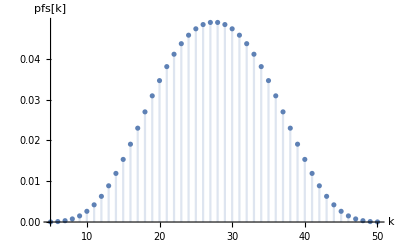

```mathematica
plotDiscrete =DiscretePlot[x4[k],{k,5,50},AxesLabel->{"k","pfs[k]"}]
```

#### Uppgift 2

För att beräkna sannolikheten att vinna så tar vi sannolikheterna att vinna och adderar de:

```mathematica
p = Sum[x4[k], {k,0,10}] + Sum[x4[k], {k,45,50}] //N
```

0.0106771

```mathematica
(1-p)^64//N
```

0.503079

#### Uppgift 3

Genom att ta 1/pså kan vi beräkna antalet kast för 100%, eller för att vinna Teddyn

```mathematica
1/p
```

93.6585

#### Uppgift 4

Genom att ta den sammanlagda summan av alla utfall (100% eller 1) och subtrahera förlustchansen för 20 kast så kan vi beräkna vinstchansen för 20 kast:

```mathematica
o =1-((1- p)^20) //N
```

0.193208

Uppgift 2: Normalfördelning

## Sammanfattning

### Uppgift

I denna uppgift ska vi fortsätta med uppgift 1 men vi ska använda normalfördelning för att svara på deluppgifterna nedan:

Bestäm förväntningsvärden och standardavvikelsern för fördelningen i Teddy-fallet.

Bestäm sannolikheten för teddypriset med normal distribution.

Jämför och kommentera resultaten mellan första och andra uppgiften.

### Resultat

#### Väntevärde och standardavvikelsern

Vi fick att väntevärdet blev:

μ = E(X) = 55/2 = 27.5

och standardavvikelsen blev:

σ = √(655/12)= 7.38805

#### Sannolikheten för teddypriset med normal distribution.

Vi behövde bara normalfördelningens sannolikhetsfunktion cdf_x(x)  för att få ut sannolikhet att man vinner en teddy.
Vi fick sannolikheten 0.015528 ≃ 1.55% för att vinna en teddy.

## Uträkning och diskussion

#### Väntevärdet och standardavvikelsern

Väntevärdet för en diskret stokastisk variable X defineras som:

μ = E(X) =∑_(∀x) x pf_X(x)

Där s.v. X är summan av ett kast och pf_X(x) är sannolikheten för att få summan X.
Med formeln fick vi väntevärdet  μ = 55/2 = 27.5  

För att få ut standardavvikelse σ måste vi först få ut variansen  σ^2:

σ^2 = E((X -μ)^2) = 
E(X^2-2Xμ + μ^2) = E(X^2) - 2E(X)μ + μ^2 = 
E(X^2) - μ^2

E(X^2) = ∑_(∀x) x^2 pf_X(x) =4865/6 ≃ 810.833

μ^2 = (27.5)^2 = 756.25

σ^2 = 4865/6  - 756.25 = 655/12  ≃ 54.5833

Om man tar roten ur variansen så får man standardavvikelsen:

σ =  √(σ^2)=  √(E(X^2) - μ^2)
σ = √(655/12)= 7.38805

#### Sannolikheten för teddypriset med normal distribution

Nu kan vi få ut normalfördelningen genom att lägga in väntevärdet och standardavvikelsen  i N(μ,σ):

φ(t)=1/(√(2π))ⅇ^(-t^2/2)

ϕ(x) = ∫_(-∞)^x φ(t)ⅆt 

pdf_t(t) =1/σ ϕ[(t-u)/σ] = (ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

cdf_x(x) =ϕ[(x-u)/σ] = 1/2 erfc((μ-x)/(√2 σ))

Då får vi ut fördelningfunktionen  P(X ≤ x) =cdf_x(x) och täthetsfunktionen P(a ≤X ≤ b) =pdf_t(t) .

Med fördelningfunktionen cdf_x(x) kan vi få ut sannolikheten att man vinner en teddy:

P(Teddy) = (cdf_x(10) -cdf_x(5)) + (cdf_x(50) -cdf_x(45))  .

P(Teddy) =0.015528 ≃1.55%.

#### Lite diskussion kring normalfördelningen

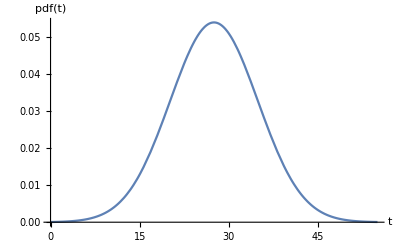
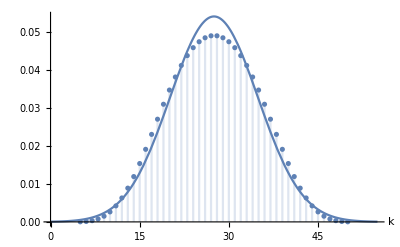
Om man ritar ut normalfördelningens täthetsfunktion så får man graf som är ganska lika diskreta fördelningen i uppgift 1:
-Graphics-

Nedan kan vi se skillnaden grafiskt mellan normalfördelningen och diskreta fördelningen:

-Graphics-

Man kan se att deras kurvor ganska nära varandra men normalfördelningen högsta punkt är lite högre än diskreta fördelningens punkt.

Hur fick vi en funktion som har nästan samma egenskaper som diskreta funktionen?

Tärningskast spelet som vi undersökte har observationsvärden som följer ett visst mönster. Många olika oberoende fenomen i naturen och samhället följer samma mönster, som kallas för normalfördelning.

Normalfördelningen ändras beroende på väntevärdet μ och standardavikelse σ.
Väntevärdet bestämmer positionen för grafens centrum och standardavvikelsen bestämmer grafens höjd, dvs. storleken på observationsvärdens utspriddning från väntevärdet.
Ju mer data man har desto närmare man får en funktion som har nästa samma egenskaper som normalfördelningen.

## Kod

### Uppgift 5

Mathematica har inbyggda funktioner för att kunna räkna ut väntevärdet och standardavvikelsen

```mathematica
Δk=1;
```

```mathematica
𝒟=ProbabilityDistribution[x4[k],{k,5,50,Δk}];
```

```mathematica
μ = Mean[𝒟]
```

55/2

```mathematica
σ = StandardDeviation[𝒟]
```

(√(655/3))/2

### Uppgift 6

Vi kan få ut normalfördelningen genom att mata in μ och σ i  Mathematicas normalfördlnings funktion.

```mathematica
n=NormalDistribution[μ,σ];
```

Nu kan vi få ut  cdf_x(x) och pdf_t(t) och plotta dem.

```mathematica
PDF[n,x]//TraditionalForm
CDF[n,x]//TraditionalForm
```

√(6/(655 π)) ⅇ^(-6/655 (x-55/2)^2)

1/2 erfc(√(6/655) (55/2-x))

```mathematica
plotNormalD = Plot[PDF[n,x],{x,0,55},PlotRange->All,
AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}]
```

-Graphics-

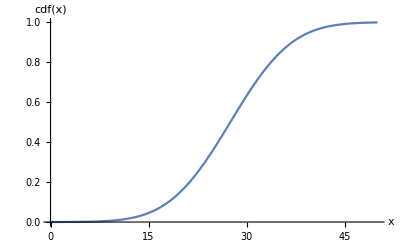

```mathematica
Plot[CDF[n,x],{x,0,50},PlotRange->All,
AxesLabel->{HoldForm[x],HoldForm[cdf[x]]}]
```

Sannolikhet att vinna en teddy:

```mathematica
CDF[n,10]-CDF[n,5]+CDF[n,50]-CDF[n,45] //N
```

0.015528

### Uppgift 7

Jämförelse mellan normalfördelningen och discketa fördelningen från första uppgiften.

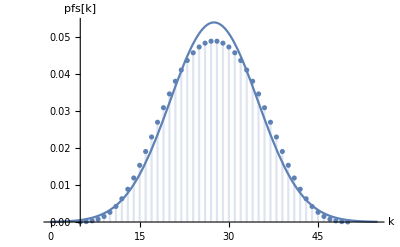

```mathematica
Show[plotDiscrete, plotNormalD, PlotRange -> Automatic]
```